# ABS Equations with Octupole

```mathematica
ClearAll["Global`*"];
```

```mathematica
w=1.0;
(*w=20.0;*)
q=20.0;
mu=-0.001;          (*octupole strength (dimensionless)*)
n=256*4;
sgrid=Subdivide[0.,1.,n-1];
ds=sgrid[[2]]-sgrid[[1]];
```

```mathematica
(*-------------------------Initial conditions-------------------------*)
a0=ConstantArray[1.0,n];
d0=ConstantArray[0.0,n];
y0=Join[a0,d0];
```

```mathematica
(*-------------------------Precompute linear operators Ds:first derivative in s (2nd order interior,2nd order one-sided at ends)-------------------------*)DsMat=SparseArray[{},{n,n}];

(*interior centered*)
DsMat+=SparseArray[Join[Table[{i,i+1}->1/(2 ds),{i,2,n-1}],Table[{i,i-1}->-1/(2 ds),{i,2,n-1}]],{n,n}];

(*forward at i=1:(-3 f1+4 f2-f3)/(2 ds)*)
DsMat+=SparseArray[{{1,1}->-3/(2 ds),{1,2}->4/(2 ds),{1,3}->-1/(2 ds)},{n,n}];

(*backward at i=n:(3 fn-4 f(n-1)+f(n-2))/(2 ds)*)DsMat+=SparseArray[{{n,n}->3/(2 ds),{n,n-1}->-4/(2 ds),{n,n-2}->1/(2 ds)},{n,n}];
```

```mathematica
(*Wake integral operator for constant wake:F=w*∫_0^s a(s') ds' with F(0)=0. Discrete:F_i=w ds*Sum_{k=1}^{i-1} a_k (or equivalently Accumulate[a]-a1) Make it a matrix:(strictly lower triangular ones)*)(*WakeMat=w ds SparseArray[Table[{i,j}->1.,{i,1,n},{j,1,i-1}],{n,n}];*)
FfromA[a_]:=w ds (Accumulate[a]-a[[1]]);
```

```mathematica
(*-------------------------RHS in theta for y={a(1..n),d(1..n)} Using x± =a±d/2,octupole term applied to each x±separately.-------------------------*)rhs[y_?VectorQ]:=Module[{a,d,as,ds1,F,xp,xm,NLp,NLm,aThetaNL,dThetaNL},
a=y[[1;;n]];
d=y[[n+1;;2 n]];
(*enforce d(theta,0)=d(theta,1)=0 strongly*)
d[[1]]=0.;
d[[-1]]=0.;
(*linear pieces*)
as=DsMat.a;
ds1=DsMat.d;
(*F=WakeMat.a;*)
F=FfromA[a];

(*x±fields*)
xp=a+0.5 d;
xm=a-0.5 d;

(*octupole nonlinearity on each stream*)
NLp=I mu (Abs[xp]^2) xp;
NLm=I mu (Abs[xm]^2) xm;

(*convert back to (a,d) equations:a=(xp+xm)/2=>a_theta_NL=(NLp+NLm)/2 d=(xp-xm)=>d_theta_NL=(NLp-NLm)*)
aThetaNL=0.5 (NLp+NLm);
dThetaNL=(NLp-NLm);

Join[(1/(2 Pi)) ds1+I F+aThetaNL,(2/Pi) as+I q d+dThetaNL]
];
```

```mathematica
(* ------------------------- Integrate in theta ------------------------- *)
solY = NDSolveValue[
  {y'[θ] == rhs[y[θ]], y[0] == y0},
  y,
  {θ, 0, 40 Pi},
  Method -> {"StiffnessSwitching"},
  AccuracyGoal -> 8,
  PrecisionGoal -> 8,
  MaxStepFraction -> 1/50
];
```

```mathematica
(*-------------------------Fast linear interpolation in s (no Interpolation[] construction per call)-------------------------*)linEval[vec_?VectorQ,s_?NumericQ]:=Module[{u,i,t},If[s<=0.,Return[vec[[1]]]];
If[s>=1.,Return[vec[[-1]]]];
u=s/ds+1;(*continuous index in[1,n]*)i=Floor[u];
If[i>=n,Return[vec[[-1]]]];
t=u-i;
(1-t) vec[[i]]+t vec[[i+1]]];
```

```mathematica
aVec[θ_?NumericQ]:=solY[θ][[1;;n]];
dVec[θ_?NumericQ]:=solY[θ][[n+1;;2 n]];

aFun[θ_?NumericQ,s_?NumericQ]:=linEval[aVec[θ],s];
dFun[θ_?NumericQ,s_?NumericQ]:=linEval[dVec[θ],s];

xpFun[θ_?NumericQ,s_?NumericQ]:=aFun[θ,s]+0.5 dFun[θ,s];
xmFun[θ_?NumericQ,s_?NumericQ]:=aFun[θ,s]-0.5 dFun[θ,s];

xcentroid[θ_?NumericQ,s_?NumericQ]:=aFun[θ,s];
```

```mathematica
logAbsXp[θ_,s_]:=Log[Abs[xpFun[θ,s]]];
logAbsXm[θ_,s_]:=Log[Abs[xmFun[θ,s]]];

argXp[θ_,s_]:=Arg[xpFun[θ,s]];
argXm[θ_,s_]:=Arg[xmFun[θ,s]];
```

```mathematica
θobs=1.5*2*Pi;
sgridPlot=Subdivide[0,1,300];

dataLogXp=Table[{s,logAbsXp[θobs,s]},{s,sgridPlot}];
dataLogXm=Table[{s,logAbsXm[θobs,s]},{s,sgridPlot}];

dataArgXp=Table[{s,argXp[θobs,s]},{s,sgridPlot}];
dataArgXm=Table[{s,argXm[θobs,s]},{s,sgridPlot}];
```

```mathematica
pLog=ListLinePlot[{dataLogXp,dataLogXm},PlotStyle->{Blue,Orange},PlotLegends->LineLegend[{"",""},LabelStyle->Directive[24]],AxesLabel->{"s","log(x)"},PlotRange->All,ImageSize->Large,BaseStyle->{FontSize->30}];
```

```mathematica
unwrap[list_]:=Module[{s=list[[All,1]],φ=list[[All,2]],dφ,φu},(*unwrap jumps*)dφ=Differences[φ];
dφ=dφ/. {x_/;x>Pi->x-2 Pi,x_/;x<-Pi->x+2 Pi};
φu=Accumulate[Prepend[dφ,φ[[1]]]];
(*wrap back into (-Pi,Pi]*)Transpose@{s,Mod[φu+Pi,2 Pi]-Pi}];

pArg=ListLinePlot[{unwrap[dataArgXp],unwrap[dataArgXm]},PlotStyle->{Green,Red},PlotLegends->LineLegend[{"arg ","arg "},LabelStyle->Directive[24]],AxesLabel->{"s","arg(x)"},PlotRange->All,ImageSize->Large,BaseStyle->{FontSize->30}];
```

```mathematica
Print[GraphicsGrid[{{pLog},{pArg}},Spacings->{0,0.6}]]
```

-Graphics-

```mathematica
(*----snapshot times in theta----*)
θ0=5.Pi;θ1=20. Pi;
m=1000;                         (*number of snapshots*)
θlist=Subdivide[θ0,θ1,m-1];
Δθ=θlist[[2]]-θlist[[1]];

yVec[θ_?NumericQ]:=Module[{y=solY[θ],a,d},a=y[[1;;n]];
d=y[[n+1;;2 n]];
d[[1]]=0.;d[[-1]]=0.;
Join[a,d]                 (*size 2n*)];

Y=Transpose@(yVec/@θlist);   (*(2n) x m*)
```

```mathematica
Y1=Y[[All,1;;-2]];
Y2=Y[[All,2;;-1]];
```

```mathematica
{Ufull,Σfull,Vfull}=SingularValueDecomposition[Y1];
σy=Diagonal[Σfull];
cum=Accumulate[σy^2]/Total[σy^2];
r=First@FirstPosition[cum,_?(#>=0.9999999&)]
```

10

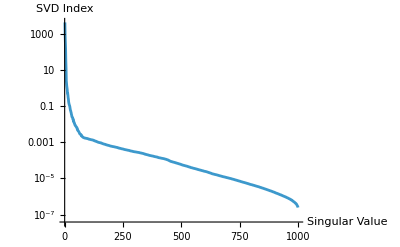

```mathematica
ListLinePlot[σy,ScalingFunctions->"Log",PlotRange->All,AxesLabel->{"Singular Value","SVD Index"}]
```

```mathematica
{U,Σ,V}=SingularValueDecomposition[Y1,r];

Σpinv=PseudoInverse[Σ];
Atilde=ConjugateTranspose[U].Y2.V.Σpinv;    (*r x r*)

{λ,W}=Eigensystem[Atilde];   (*λ:length r,W:r x r (vecs as rows or cols?)*)

Λ=DiagonalMatrix[λ];
Wmat=Transpose[W];            (*make eigenvectors columns*)
Φ=Y2.V.Σpinv.Wmat;            (*(2n) x r*)

ω=Log[λ]/Δθ;
growth=Re[ω];
freq=Im[ω];    (*rad per theta*)

y1=Y[[All,1]];
b=LeastSquares[Φ,y1];
```

```mathematica
yHat[j_Integer]:=Φ.(b*(λ^j));     (*(2n)-vector*)

(*example:compare snapshot j*)
jtest=200;
relErrJ=Norm[yHat[jtest]-Y[[All,jtest+1]]]/Norm[Y[[All,jtest+1]]];
relErrJ
```

0.02476

```mathematica
Dimensions/@{Y1,U,Σ,V,Atilde,Φ}
```

{{2048,999},{2048,10},{10,10},{999,10},{10,10},{2048,10}}

```mathematica
Φa=Φ[[1;;n,All]];          (*centroid/‘a’ part of modes*)
Φd=Φ[[n+1;;2 n,All]];      (*‘d’ part of modes*)
```

```mathematica
jmax=Dimensions[Y][[2]]-1;
errs=Table[With[{ytrue=Y[[All,j+1]],yhat=Φ.(b*(λ^j))},Norm[yhat-ytrue]/Norm[ytrue]],{j,0,jmax}];
```

{0.0642007,0.291114}

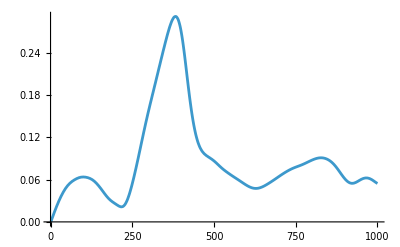

```mathematica
{Median[errs],Max[errs]}
ListLinePlot[errs,PlotRange->All]
```

```mathematica
(*----Look at importance of modes----*)
impA=Abs[b]*(Norm/@Transpose[Φa]);          (*length r*)
impASorted=Reverse@Sort[impA];
kordered = Reverse[Ordering[impA]];
```

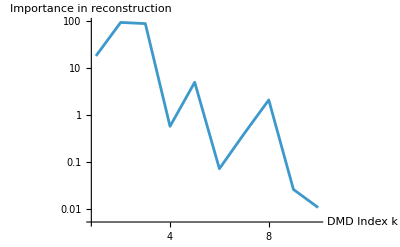

```mathematica
ListLinePlot[Transpose@{Range[r],impA},PlotRange->All,ScalingFunctions->{"Linear","Log"},AxesLabel->{"DMD Index k","Importance in reconstruction"}]
```

```mathematica
(*----snapshot times in theta----*)
θref=θ0;   

timeFactor[k_Integer,θ_?NumericQ]:=b[[k]]*Exp[ω[[k]]*(θ-θref)];

nTurns=23;
θstrobes=θref+2 Pi Range[0,nTurns];

modeA[k_Integer]:=Interpolation[Transpose[{sgrid,Φa[[All,k]]}],InterpolationOrder->1];

(* Calculate amplification coefficients *)
amplificationks = Table[Abs[modeA[l][1]/modeA[l][0]],{l,Range[r]}];

modeContribution[k_Integer,θ_?NumericQ,s_?NumericQ]:=Re[modeA[k][s]*timeFactor[k,θ]];
```

```mathematica
plots=Table[
ListLinePlot[Table[Table[{s,modeContribution[k,θ,s]},{s,sgrid}],{θ,θstrobes}],
PlotStyle->Directive[Black,Thick],PlotRange->All,AxesLabel->{"s",None},
PlotLabel->Row[{"k=",k,",  Importance=",ScientificForm[impA[[k]],3],", Amplification=",NumberForm[amplificationks[[k]],{3,3}]}]],{k,kordered}
];
```

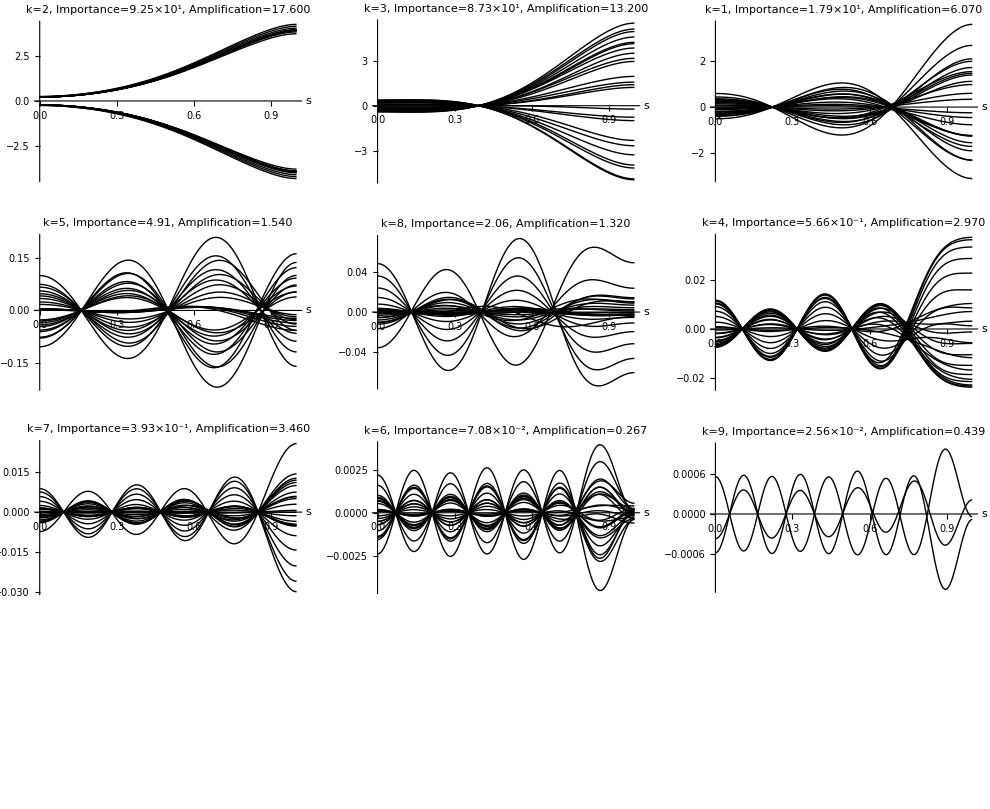

```mathematica
GraphicsGrid[Partition[plots,UpTo[3]]]
```

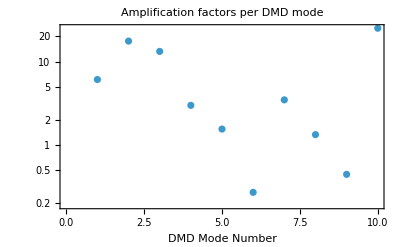

```mathematica
(* Plot amplification factors *)
ListLogPlot[Transpose[{kordered,amplificationks[[kordered]]}],
Frame->{True,True,False,False},
FrameLabel->{Style["DMD Mode Number", Black, Large],""}, LabelStyle->Directive[Larger,Black],
PlotLabel->Style["Amplification factors per DMD mode", Black, Larger], PerformanceGoal->"Speed"]
```